```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Functions *)
KP[A_,B_]:=KroneckerProduct[A,B]
KPfromBits[l_]:=Flatten[Apply[KP,l /. {0->{1,0},1->{0,1}}]]
UnifromSuperposFromBits[bitvectors__]:=Module[{v},
SumVectorsFromBits[bits_]:=KPfromBits[bits];
SumVectorsFromBits[bits_,list__]:=KPfromBits[bits]+SumVectorsFromBits[list];
v=SumVectorsFromBits[bitvectors];
1/Sqrt[Total[Unitize[v]]]*Unitize[v]
]
UviaSVD[S_,T_]:=Module[{M,U,Σ,V},
M=T.ConjugateTranspose[S];
{U,Σ,V}=SingularValueDecomposition[M];
U.ConjugateTranspose[V]
]
```

```mathematica
(* The vectors we want to map *)
```

```mathematica
v1 = UnifromSuperposFromBits[
{0,0},
{1,0}
];
v2 = UnifromSuperposFromBits[
{0,0},
{1,1}
];
v3 = UnifromSuperposFromBits[
{0,1},
{1,0}
];
v4 = UnifromSuperposFromBits[
{0,1},
{1,1}
];
```

```mathematica
(* Source matrix *)
S=Transpose[{v1,v2,v3,v4}];
```

```mathematica
(* Target Matrix. This is just a test, we already now that the operator is I⊗X, that is a not gate on the second qubit *)
T = Transpose[{v4,v3,v2,v1}];
```

```mathematica
U=UviaSVD[S,T];
UnitaryMatrixQ[U]
```

True

```mathematica
U.S==T
```

True

```mathematica
U//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
(* Now let's try the case of mapping v1 to v2, and v3 to v4. Here the result should be CX, a controlled not from the first qubit to the second *)
```

```mathematica
T = Transpose[{v2,v1,v4,v3}];
```

```mathematica
U=UviaSVD[S,T];
U.S==T
U//MatrixForm
```

True

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
CX=U;
```

```mathematica
(* Now we map v1 to v3, and v2 to v4. Here the result should be (X⊗I)CX *)
T = Transpose[{v3,v4,v1,v2}];
U=UviaSVD[S,T];
U.S==T
U//MatrixForm
```

True

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
ConjugateTranspose[S].S==ConjugateTranspose[T].T
```

True

```mathematica
(* Now let's try something different, like a circular permutation v1,v2,v3,v4 -> v2,v3,v4,v1 *)
```

```mathematica
T = Transpose[{v2,v3,v4,v1}];
U=UviaSVD[S,T];
U.S==T
U//MatrixForm
```

False

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
ConjugateTranspose[S].S==ConjugateTranspose[T].T
```

False

```mathematica
T//MatrixForm
U.S//MatrixForm
```

(1/(√2) | 0 | 0 | 1/(√2)
0 | 1/(√2) | 1/(√2) | 0
0 | 1/(√2) | 0 | 1/(√2)
1/(√2) | 0 | 1/(√2) | 0)

(1/(√2) | 1/(√2) | 0 | 0
0 | 0 | 1/(√2) | 1/(√2)
0 | 1/(√2) | 0 | 1/(√2)
1/(√2) | 0 | 1/(√2) | 0)

```mathematica
(* Let's check the angles among our vectors. *)
v1.v2
v2.v3
v3.v4
v4.v1
```

1/2

0

1/2

0

```mathematica
(* It make sense that we don't have a proper solution, angles are not preserved by this permutation. *)
```

```mathematica
(* Let's check all angles and see what we can afford to do. *)
v1.v2
v1.v3
v1.v4
v2.v3
v2.v4
v3.v4
```

1/2

1/2

0

0

1/2

1/2

```mathematica
(* Mappings v1<->v4 and v2<->v3 are the ones performed by the I⊗X unitary, and are not compatible with the others. *)
(* Let's try then v1,v2,v3,v4 -> v2,v4,v3,v1 *)
```

```mathematica
T = Transpose[{v2,v4,v3,v1}];
U=UviaSVD[S,T];
U.S==T
U//MatrixForm
```

False

(2/3 | 2/3 | 0 | -1/3
0 | 0 | 1 | 0
-1/3 | 2/3 | 0 | 2/3
2/3 | -1/3 | 0 | 2/3)

```mathematica
U.S//MatrixForm
```

((√2)/3 | -1/(3 √2)+(√2)/3 | (√2)/3 | -1/(3 √2)+(√2)/3
1/(√2) | 0 | 1/(√2) | 0
-1/(3 √2) | -1/(3 √2)+(√2)/3 | (√2)/3 | (2 √2)/3
(√2)/3 | (2 √2)/3 | -1/(3 √2) | -1/(3 √2)+(√2)/3)

```mathematica
T//MatrixForm
```

(1/(√2) | 0 | 0 | 1/(√2)
0 | 1/(√2) | 1/(√2) | 0
0 | 0 | 1/(√2) | 1/(√2)
1/(√2) | 1/(√2) | 0 | 0)

```mathematica
(* Let's try with less vectors v1,v4 -> v2,v3 *)
```

```mathematica
S= Transpose[{v1,v4}];
T = Transpose[{v2,v3}];
U=UviaSVD[S,T];
U.S==T
U//MatrixForm
```

True

(1/2 | 1/2 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | 1/2
-1/2 | 1/2 | 1/2 | 1/2
1/2 | -1/2 | 1/2 | 1/2)

```mathematica
ConjugateTranspose[S].S==ConjugateTranspose[T].T
```

True

```mathematica
(* One more vector v1,v2,v4 -> v2,v4,v3 *)
```

```mathematica
S= Transpose[{v1,v2,v4}];
T = Transpose[{v2,v4,v3}];
U=FullSimplify[UviaSVD[S,T]];
U.S==T
```

True

```mathematica
(* Necessary and Sufficient Condition *)
```

```mathematica
ConjugateTranspose[S].S==ConjugateTranspose[T].T
```

True

```mathematica
U//MatrixForm
```

(1/2 | 1/2 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | 1/2
-1/2 | 1/2 | 1/2 | 1/2
1/2 | -1/2 | 1/2 | 1/2)

```mathematica
S= Transpose[{v1,v2}];
T = Transpose[{v1,v3}];
U=UviaSVD[S,T];
U.S==T
U//MatrixForm
```

True

(1/3 | -1/(√3) | 2/3 | -1/3
1/3 | -1/(√3) | -1/3 | 2/3
2/3 | 1/(√3) | 1/3 | 1/3
-1/(√3) | 0 | 1/(√3) | 1/(√3))

```mathematica
U.v1==v1
```

True

```mathematica
U.v2==v3
```

True

```mathematica
U.v3//FullSimplify
```

{-(-2+√3)/(3 √2),-1/3 √(2+√3),(√(2+√3))/3,1/(√6)}

```mathematica
U.v4//FullSimplify
```

{-1/3 √(2+√3),-(-2+√3)/(3 √2),(√(2+√3))/3,1/(√6)}

```mathematica
(U.v3).(U.v4)//FullSimplify
```

1/2

```mathematica
S= Transpose[{U.v3,U.v4}];
T = Transpose[{U.v4,U.v3}];
W=UviaSVD[S,T];
```

```mathematica
(W.(U.v3//FullSimplify)//FullSimplify)==(U.v4//FullSimplify)
```

True

```mathematica
(U.v3).(U.v4)//FullSimplify
```

1/2

```mathematica
U12=MatrixPower[U,12];
```

```mathematica
data=Table[N[MatrixPower[U,i,v3].v4],{i,0,12}]
```

{0.5,-0.166667,0.722222,0.203704,0.00617284,0.788066,-0.0569273,0.287837,0.673144,-0.185363,0.574006,0.420021,-0.134035}

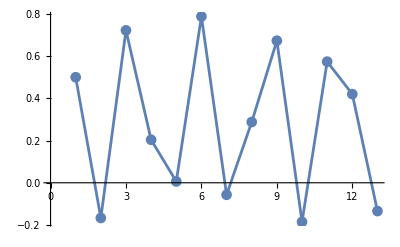

```mathematica
ListLinePlot[data,PlotMarkers->Automatic]
```

```mathematica
data2 = Table[N[(U12.MatrixPower[U,i,v3]).v4],{i,1,8}]
```

{0.758692,0.122446,0.0780473,0.773491,-0.109369,0.372334,0.612924,-0.189565}

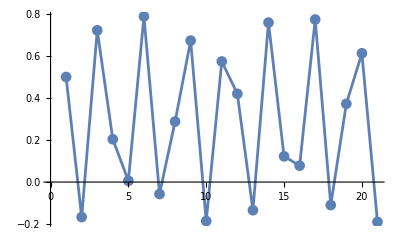

```mathematica
ListLinePlot[Join[data,data2],PlotMarkers->Automatic]
```